# Canonical Scalar Field Inflation In The Presence Of A Chern-Simons Term.

## Chaotic Inflation With An Oscillating Chern-Simons Scalar Coupling Function.

## 1.Designation Of Scalar Functions, Equations Of Motion, Slow-Roll/Observed Indices.

We start by designating the scalar functions of the model. For simplicity, the Chern-Simons scalar coupling function obtains a trigonometric form and the scalar field a power-law form. Compatibility is achieved for a quadratic potential but we shall keep it arbitrary for the time being so as to study the dependence of the observed indices, and especially the tensor spectral index nt on such exponent. The equations of motion are extracted by assuming the slow-roll condition is valid. Slow-roll indices along with observed indices are taken from arXiv:0412126.

```mathematica
v[φ_]:=Λ1 Sin[φ/φ1]
vdot[φ_]:=D[v[φ],φ]φdot[φ]
V[φ_]:=V1(κ φ)^n
H2[φ_]:=κ^2V[φ]/3
H[φ_]:=Sqrt[H2[φ]]
φdot[φ_]:=-D[V[φ],φ]/(3H[φ])
Hdot[φ_]:=-1/2κ^2φdot[φ]^2
Qt[λ_,φ_]:=1/κ^2+2λ vdot[φ]H[φ]
ε1[φ_]:=-Hdot[φ]/H2[φ]
ε2[φ_]:=ε1[φ]-D[V[φ],{φ,2}]/(κ^2V[φ])
ε6[φ_]:=D[Qt[1,φ],φ]φdot[φ]/(2H[φ]Qt[1,φ])+D[Qt[-1,φ],φ]φdot[φ]/(2H[φ]Qt[-1,φ])
ns[φ_]:=1-2(2ε1[φ]+ε2[φ])
nt[φ_]:=-2(ε1[φ]+ε6[φ])
r[φ_]:=8Abs[ε1[φ]](1/Abs[κ^2Qt[1,φ]]+1/Abs[κ^2Qt[-1,φ]])
```

## 2. Extracting The Values Of The Scalar Field.

To study the inflationary era, one needs to insert as an input the value of the scalar field during the first horizon crossing to the observed indices. Such a value can be extracted by firstly finding the final value during the ending stage of the inflationary era by imposing that ε1 becomes of order O(1). Afterwards, by using the e-folding number N=∫ Hdt, the initial value can be extracted as a function of N and φf.

```mathematica
U1=Solve[ε1[φ]==1,φ];
φf=φ/.U1[[2]]/.C[1]->0;
L1=Integrate[H[φ]/φdot[φ],φ]/.φ->φl;
L2=Integrate[H[φ]/φdot[φ],φ]/.φ->φk;
U2=Solve[N0==L1-L2,φk];
φi=φk/.U2[[2]]/.{C[1]->0,φl->φf};
```

## 3. Designation Of Free Parameters And Validity Of Approximations.

### 3.1. Derivation Of Observed Indices.

By assigning numerical values to the free parameters of the model, the initial value of the scalar field during the first horizon crossing is extracted. Subsequently, one can use such value as an input on the observed indices and derive results. Here, a blue shifted tensor spectral index (nt>0) can be achieved under the slow-roll assumption due to the presence of the Chern-Simons term in the initial gravitational action.

```mathematica
κ=1/Mp;Mp=1.2 10^(27); Λ1=1.;V1=Mp ^4;N0=60.;n=2.;φ1=Mp;
φi//N
φf//N
ns[φ]/.φ->φi//N
nt[φ]/.φ->φi//N
r[φ]/.φ->φi//N
```

1.86676×10^28

1.69706×10^27

0.966942

0.0394191

0.00646447

### 3.2. Ascertaining The Validity Of The Approximations.

The numerical values of the slow-roll indices during the first horizon crossing according to Planck 2018 data must be of order O(10^-3) and lesser. Such results are indicative of the validity of the slow-roll approximations. Slow-roll index ε6 is excluded in this case.

```mathematica
ε1[φ]/.φ->φi//N
ε2[φ]/.φ->φi//N
ε6[φ]/.φ->φi//N
```

0.00826446

2.92943×10^-18

-0.027974

Such result is also expected to apply on the self check on the equations of motion.

```mathematica
Hdot[φ]/.φ->φi//N
H2[φ]/.φ->φi//N
φdot[φ]^2/2/.φ->φi//N
V[φ]/.φ->φi//N
D[φdot[φ],φ]/.φ->φi//N
H[φ]φdot[φ]/.φ->φi//N
```

-9.6×10^53

1.1616×10^56

1.3824×10^108

5.01811×10^110

1.71799×10^10

-1.79209×10^82

## 4. Diagrammatic Results.

In this section, it is interesting to examine the area of values for certain auxiliary parameters that result in both a compatible with the observations result and also a blue shifted tensor spectral index.

```mathematica
Clear[V1];Clear[φ1];
ContourPlot[Evaluate[nt[φ]/.φ->φi],{V1,Mp^4,2 Mp^4},{φ1,0.95Mp,1.05Mp},PlotLegends->True,FrameLabel->{Subscript["V",1],Subscript["φ",1]}]
ContourPlot[Evaluate[r[φ]/.φ->φi],{V1,1Mp^4,2Mp^4},{φ1,0.95Mp,1.05Mp},PlotLegends->True,FrameLabel->{Subscript["V",1],Subscript["φ",1]}]
```

-Graphics-

-Graphics-

The scalar spectral index is independent of the Chern-Simons scalar coupling function thus for the quadratic model, only the e-folding number affects its value. Other exponents for the scalar potential are also plausible however they must reside near the value of n=2 in order to be in agreement with experiments.

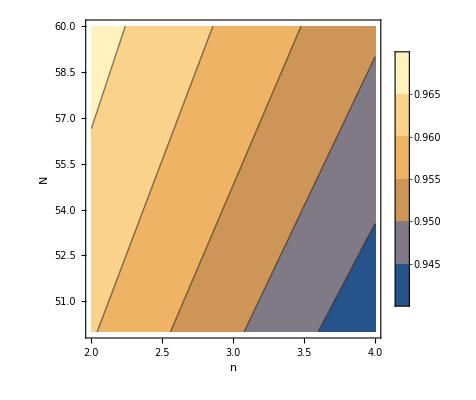

```mathematica
Clear[n];Clear[N0];V1=Mp^4;φ1=Mp;
ContourPlot[Evaluate[ns[φ]/.φ->φi],{n,2,4},{N0,50,60},PlotLegends->True,FrameLabel->{"n","N"}]
```

## 5. Root Of The Tensor Spectral Index.

As a final step, we extract the root of the tensor spectral index which marks the transition value from a blue shifted to a red shifted spectral index.

```mathematica
Clear[φ1];N0=60;n=2.;
U3=Evaluate[nt[φ]/.φ->φi];
U4=FindRoot[U3==0,{φ1,0.99Mp}];
φroot=φ1/.U4[[1]];
U3/.φ1->φroot;
Print[%]
Print[φroot/Mp]
```

-6.07153×10^-17

0.990339